```mathematica
?SparseArray`MinimumBandwidthOrdering
```

```mathematica
?SparseArray`*Bandwidth*
```

```mathematica
Needs["GraphUtilities`"]
```

```mathematica
mat=SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1,{1,-1}->1,{-1,1}->1},{1,1}6];
mat//MatrixForm
{r1,r2}=SparseArray`MinimumBandwidthOrdering[mat,Method->(*"Sloan"*)]
MinimumBandwidthOrdering[mat//Normal]
```

(0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0)

{{2,9},{{4,3,5,2,6,1},{4,3,5,2,6,1}}}

{{4,5,3,6,2,1},{4,5,3,6,2,1}}

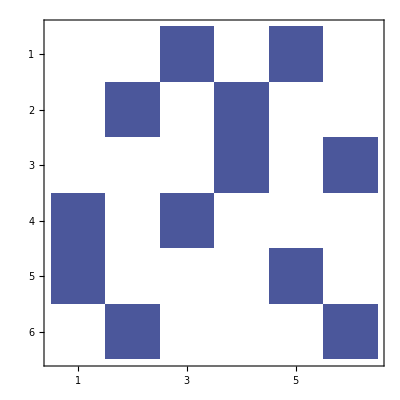

```mathematica
mat[[#]]&@@r2//MatrixPlot
```

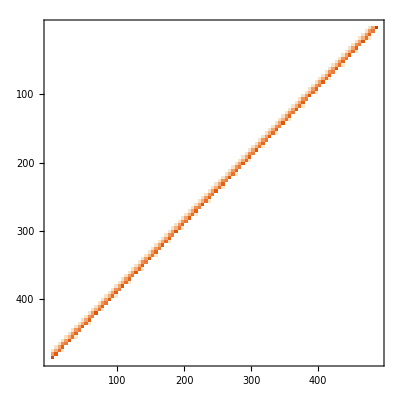

```mathematica
hBloch1DZZ[.1][[#]]&@@((*SparseArray`*)MinimumBandwidthOrdering[hBloch1DZZ[.1],Method->"RCMD"(*"Sloan"*)](*[[2]]*))//MatrixPlot
```

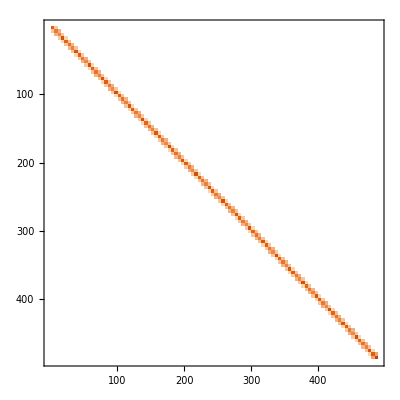

```mathematica
hBloch1DZZ[.1]//MatrixPlot
```

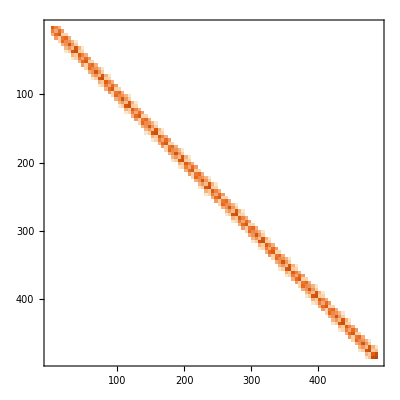

```mathematica
hBloch1DAC[.1]//MatrixPlot
```

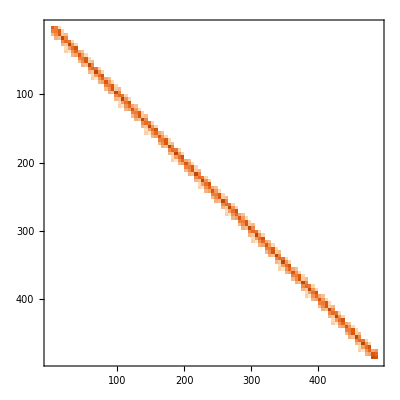

```mathematica
hBloch1DAC[.1][[#]]&@@((*SparseArray`*)MinimumBandwidthOrdering[hBloch1DAC[.1],Method->"RCMD"(*"Sloan"*)](*[[2]]*))//MatrixPlot
```

```mathematica
?SparseArray`*
```

```mathematica
SparseArray`NestedDissection[hBloch1DAC[.1]]
(*hBloch1DAC[.1][[#]]&@@%//MatrixPlot*)
```

{240,239,128,127,236,235,132,131,230,229,220,219,214,213,204,203,198,197,188,187,182,181,172,171,166,165,156,155,150,149,234,233,122,121,133,129,134,130,135,139,136,140,142,138,237,225,141,137,143,144,232,226,231,238,151,147,223,227,145,146,148,152,218,217,224,228,153,157,209,221,160,154,158,159,216,210,215,222,167,163,207,211,162,161,164,168,202,201,208,212,169,173,193,205,176,170,174,175,200,194,199,206,183,179,192,196,178,177,180,184,185,186,189,190,191,195,118,117,6,5,106,105,2,1,104,103,94,93,84,83,78,77,68,67,62,61,52,51,46,45,36,35,30,29,20,19,116,115,4,3,7,8,13,14,11,15,111,107,10,9,12,16,110,108,109,112,97,98,99,100,101,89,17,21,96,90,95,102,24,18,22,23,87,91,31,27,82,81,88,92,26,25,28,32,73,85,33,37,80,74,79,86,40,34,38,39,71,75,47,43,66,65,72,76,42,41,44,48,57,69,50,54,64,49,53,55,56,58,59,60,63,70,120,124,114,113,126,125,119,123,366,365,254,253,354,353,250,249,352,351,342,341,332,331,326,325,316,315,310,309,300,299,294,293,284,283,278,277,268,267,364,363,252,251,255,256,261,262,259,263,359,355,258,257,260,264,358,356,357,360,345,346,347,348,349,337,265,269,344,338,343,350,272,266,270,271,335,339,279,275,330,329,336,340,274,273,276,280,321,333,281,285,328,322,327,334,288,282,286,287,319,323,295,291,314,313,320,324,290,289,292,296,305,317,298,302,312,297,301,303,304,306,307,308,311,318,488,487,376,375,484,483,380,379,478,477,468,467,462,461,452,451,446,445,436,435,430,429,420,419,414,413,404,403,398,397,482,481,370,369,381,377,382,378,383,387,384,388,390,386,485,473,389,385,391,392,480,474,479,486,399,395,471,475,393,394,396,400,466,465,472,476,401,405,457,469,408,402,406,407,464,458,463,470,415,411,455,459,410,409,412,416,450,449,456,460,417,421,441,453,424,418,422,423,448,442,447,454,431,427,440,444,426,425,428,432,433,434,437,438,439,443,368,372,367,362,373,361,374,371,244,242,245,248,243,247,246,241}